## Load package

```mathematica
SetDirectory[NotebookDirectory[]];
<<"ExtFileLoading.wl";
```

```mathematica
<<"DegFileNaming.wl";
```

```mathematica
Remove[fAttrValFunc]
```

```mathematica
<<"ArrayManip.wl";
```

```mathematica
<<"PlotMatexFormatting.wl";
SetDirectory[NotebookDirectory[]<>"/.."];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"ExtFileLoading.wl";
SetDirectory[NotebookDirectory[]<>"/.."];
```

StartExternalSession::help: For help configuring the Julia evaluator, see Configure Julia for ExternalEvaluate.

StartExternalSession::replFail: The process for external system Julia (C:\Users\Ohdraw.niL\AppData\Local\Programs\Julia-1.7.3\bin\julia.exe) failed to start.

ExternalEvaluate::unknownSys: … is not a known system in the ExternalEvaluate Framework.

## Params, labels

### Styling

```mathematica
lineStyleLst=lineStyleLstFunc[colorLst,dataThick];
```

### Params

```mathematica
m0=10;
```

```mathematica
mSz=10;
nDim=3;
itNum=10;
divLst=Floor[{128,128,16}√(mSz/m0)];
seed=1000;
```

### Labels

```mathematica
xyLabs2d=MaTeX["\\theta_"<>ToString[#]<>"/2\\pi",Magnification->labMag]&/@{1,2};
```

```mathematica
pltMLstTitles=MaTeX["M="<>ToString[#],Magnification->titleMag]&/@mLst;
```

## Single plots

### Plot ticks, labels etc

```mathematica
ticks01=Table[{tx,NumberForm[tx,{1,1}]},{tx,0,1,0.2}];
```

```mathematica
xyLabs=MaTeX["\\theta_"<>ToString[#]<>"/2\\pi",Magnification->labMag]&/@{1,2};
```

```mathematica
plotZakFun[arr_,imSz_]:=MatrixPlot[arrᵀ,PlotRangePadding->None,DataRange->{{0,1},{0,1}},DataReversed->False,ImageSize->imSz cm,FrameTicks->{{ticks01,False},{ticks01,False}},FrameLabel->Reverse[xyLabs],BaseStyle->texStyle];
```

```mathematica
xyLabs
```

{-Graphics-,-Graphics-}

```mathematica
divLst
```

{181,181,22}

```mathematica
fMain="deg_GOE3";
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fMod="";
fName=fNameFun[fMain,attrLstDim,valLstDim,fMod,jld2Type];
```

```mathematica
fName
```

deg_GOE3_dim_3_N_20_param_divide_[181, 181, 22]_instanceNum_5_seed_1000_test.jld2

```mathematica
zakLstLst=readJuliaVarSqDim[fName,"zakLstLst"];
```

```mathematica
zakLstLst//Dimensions
```

{5,181,181,20}

```mathematica
zakLstLst⟦1,1,2⟧
```

0.

```mathematica
ticks01=Table[{tx,NumberForm[tx,{1,1}]},{tx,0,1,0.2}];
```

```mathematica
ticks01
```

{{0.,0.0},{0.2,0.2},{0.4,0.4},{0.6,0.6},{0.8,0.8},{1.,1.0}}

```mathematica
ticks01[[1]]
```

0.0

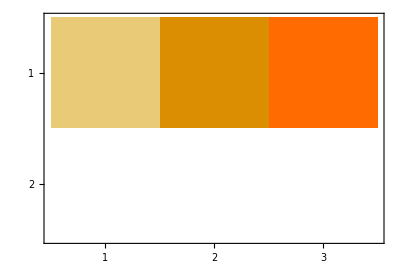

```mathematica
MatrixPlot[{{1,2,3},{0,0,0}}]
```

```mathematica
NumberForm[ticks01,{1,1}]
```

{0.0,0.2,0.4,0.6,0.8,1.0}

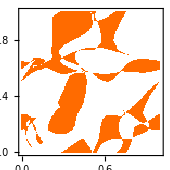

```mathematica
Show[plotZakFun[zakLstLst⟦1,All,All,1⟧,6],PlotLabel->pltTitles⟦1⟧]
```

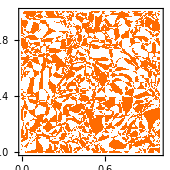

```mathematica
MatrixPlot[zakLstLst⟦1,All,All,9⟧ᵀ,PlotRangePadding->None,DataRange->{{0,1},{0,1}},DataReversed->False,ImageSize->6cm,FrameTicks->{{ticks01,False},{ticks01,False}},FrameLabel->Reverse[xyLabs],BaseStyle->texStyle]
```

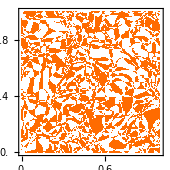
```mathematica
plotZak=-Graphics-
```

-Graphics-

```mathematica
Export[figDirStr<>"zakGOEsample.pdf",]
```

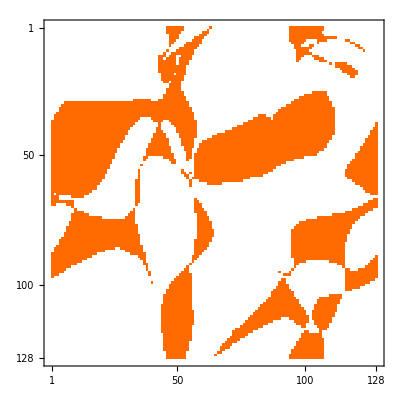

```mathematica
MatrixPlot[zakLstLst⟦1,All,All,1⟧,PlotRangePadding->None]
```

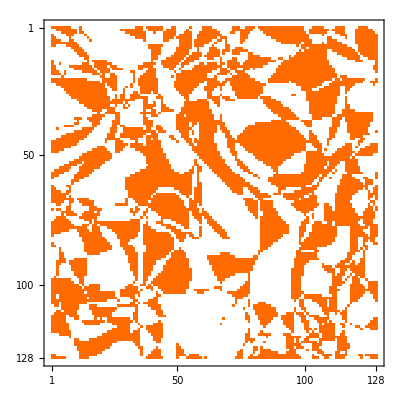

```mathematica
MatrixPlot[zakLstLst⟦1,All,All,4⟧,PlotRangePadding->None]
```

```mathematica
fMain="zakCorrStats";
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fMod="testarr";
fName=fNameFun[fMain,attrLstDim,valLstDim,fMod,jld2Type];
```

```mathematica
fName
```

zakCorrStats_dim_3_N_20_param_divide_[181, 181, 22]_instanceNum_5_seed_1000_testarr.jld2

```mathematica
zakCorrArr=readJuliaVar[fName,"zakCorrArr"];
```

```mathematica
zakCorrAvg=readJuliaVarSq[fName,"zakCorrArrAvg"];
```

```mathematica
zakCorrStd=readJuliaVarSq[fName,"zakCorrArrStd"];
```

```mathematica
zakCorrAvg//Dimensions
```

```mathematica
zakCorrArr//Dimensions
```

{10,128,128,10}

```mathematica
zakCorrAvg⟦1,3,1⟧
```

0.

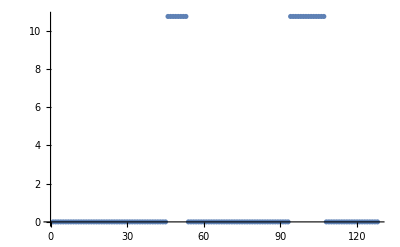

```mathematica
ListPlot[zakCorrArr⟦1,1,All,1⟧]
```

```mathematica
zakCorrAvg//Dimensions
```

{1,128,128,10}

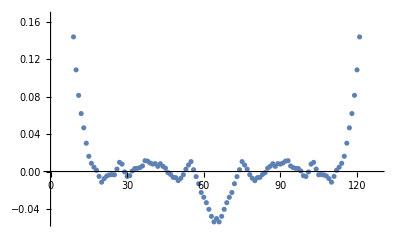

```mathematica
ListPlot[zakCorrAvg⟦All,1,4⟧]
```

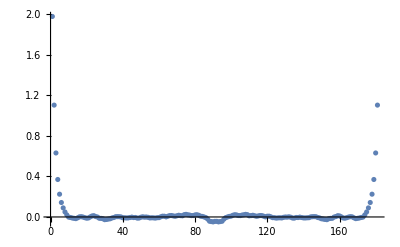

```mathematica
ListPlot[zakCorrAvg⟦All,1,9⟧,PlotRange->All]
```

```mathematica
Total[zakCorrAvg⟦All,1,4⟧]
```

10.8247

```mathematica
Total[zakCorrArr⟦3,All,1,4⟧]/divLst⟦1⟧
```

0.0545158

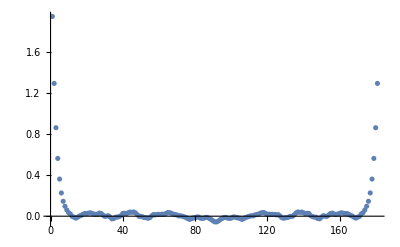

```mathematica
ListPlot[zakCorrArr⟦3,All,1,4⟧,PlotRange->All]
```

```mathematica
ListPlot[zakCorrAvg⟦All,1,4⟧]
```

-Graphics-

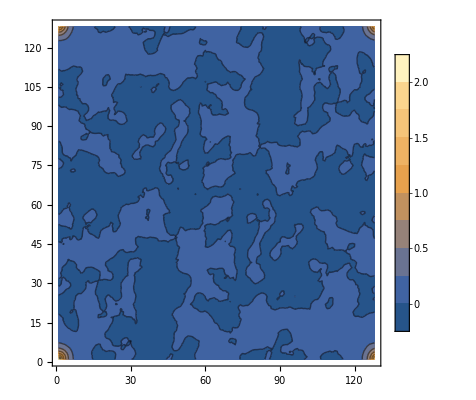

```mathematica
ListContourPlot[zakCorrAvg⟦All,All,4⟧,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
zakCorrAvg⟦1;;5,1;;5,1⟧
```

{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

```mathematica
(2π)^2//N
```

39.4784

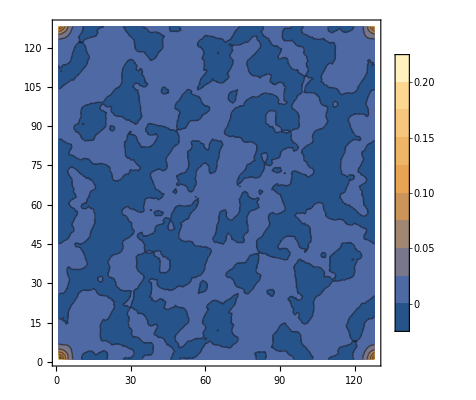

```mathematica
ListContourPlot[zakCorrAvg⟦All,All,4⟧((2π)/128)^2,PlotRange->All,PlotLegends->Automatic]
```

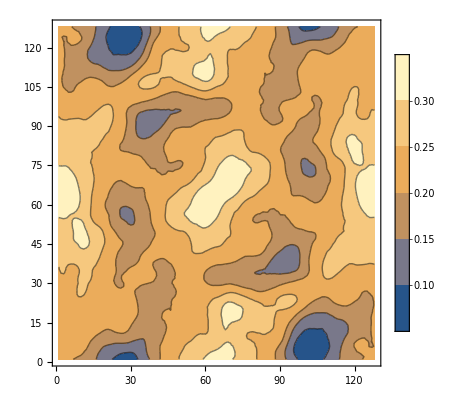

```mathematica
ListContourPlot[zakCorrStd⟦All,All,1⟧,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Total[{{1,2,3},{4,5,6}}]
```

{5,7,9}

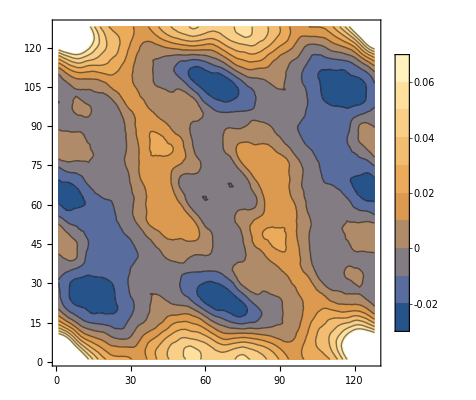

```mathematica
ListContourPlot[Total[zakCorrArr⟦All,All,All,1⟧]/itNum,PlotLegends->Automatic]
```

```mathematica
zakCorrArr//Dimensions
```

{5,181,181,20}

```mathematica
zakCorrArr⟦1,1;;3,1;;3,1⟧
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
ListContourPlot[zakCorrArr⟦1,All,All,9⟧,PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
ListContourPlot[zakLstLst⟦9,All,All,4⟧]
```

-Graphics-

## Multiple Zak plots

```mathematica
fMain="deg_GOE3";
```

```mathematica
m0=10;
```

```mathematica
nDim=3;
itNum=10;
divLst0={128,128,16};
seed=1000;
fMod="";
```

```mathematica
mLst=Table[m,{m,10,60,5}];
mLn=Length[mLst];
```

```mathematica
divLstMLst=Table[Floor[divLst0 √(mLst⟦iM⟧/m0)],{iM,1,mLn}];
```

```mathematica
xLstMLst=Table[Table[(2π)/Floor[√(mLst⟦iM⟧/m0)divLst0⟦1⟧](iX-1/2),{iX,1,divLstMLst⟦iM⟧⟦1⟧}]//N,{iM,1,mLn}];
```

```mathematica
divLstMLst//MatrixForm
```

(128 | 128 | 16
156 | 156 | 19
181 | 181 | 22
202 | 202 | 25
221 | 221 | 27
239 | 239 | 29
256 | 256 | 32
271 | 271 | 33
286 | 286 | 35
300 | 300 | 37
313 | 313 | 39)

```mathematica
pltTitles=MaTeX["M="<>ToString[#],Magnification->titleMag]&/@mLst;
```

```mathematica
pltTitles
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fName
```

zakCorrStats_dim_3_N_35_param_divide_[239, 239, 29]_instanceNum_10_seed_1000__itStop_1.jld2

```mathematica
zakLstMLst=ConstantArray[0,mLn];
```

```mathematica
For[iM=3,iM<=3,iM++,
mSz=mLst⟦iM⟧;
divLst=Floor[divLst0 √(mSz/m0)];
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fName=fNameFun[fMain,attrLstDim,valLstDim,fMod,jld2Type];
zakLstMLst⟦iM⟧=readJuliaVarSqDim[fName,"zakLstLst"];
]
```

```mathematica
plotZakFun[zakLstMLst⟦3⟧⟦10,All,All,8⟧,6]
```

-Graphics-

```mathematica
For[iM=1,iM<=mLn,iM++,
mSz=mLst⟦iM⟧;
divLst=Floor[divLst0 √(mSz/m0)];
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fName=fNameFun[fMain,attrLstDim,valLstDim,fMod,jld2Type];
zakLstLst=readJuliaVarSqDim[fName,"zakLstLst"];
mRat=Floor[0.4mSz];
fig=plotZakFun[zakLstLst⟦1,All,All,mRat⟧,6];
Print[Show[fig,PlotLabel->pltTitles⟦iM⟧]]
]
```

-Graphics-

-Graphics-

-Graphics-

«6 more identical outputs»

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[$Aborted,{}].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

MatrixPlot::mat0: Argument Transpose[Symbol[]] at position 1 is not a matrix.

Show::gtype: MatrixPlot is not a type of graphics.

Show[MatrixPlot[Transpose[Symbol[]],PlotRangePadding→None,DataRange→{{0,1},{0,1}},DataReversed→False,ImageSize→170.079,FrameTicks→{{{{0.,0.0},{0.2,0.2},{0.4,0.4},{0.6,0.6},{0.8,0.8},{1.,1.0}},False},{{{0.,0.0},{0.2,0.2},{0.4,0.4},{0.6,0.6},{0.8,0.8},{1.,1.0}},False}},FrameLabel→{-Graphics-,-Graphics-},BaseStyle→{FontFamily→Times New Roman,FontSize→8,FontWeight→Plain}],PlotLabel→-Graphics-]

ExternalEvaluate::invalidSession: The session … is invalid and cannot be used.

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[$Failed,{}].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

MatrixPlot::mat0: Argument Transpose[Symbol[]] at position 1 is not a matrix.

Show::gtype: MatrixPlot is not a type of graphics.

Show[MatrixPlot[Transpose[Symbol[]],PlotRangePadding→None,DataRange→{{0,1},{0,1}},DataReversed→False,ImageSize→170.079,FrameTicks→{{{{0.,0.0},{0.2,0.2},{0.4,0.4},{0.6,0.6},{0.8,0.8},{1.,1.0}},False},{{{0.,0.0},{0.2,0.2},{0.4,0.4},{0.6,0.6},{0.8,0.8},{1.,1.0}},False}},FrameLabel→{-Graphics-,-Graphics-},BaseStyle→{FontFamily→Times New Roman,FontSize→8,FontWeight→Plain}],PlotLabel→-Graphics-]

## Fitting plots

### Params, file names, etc

```mathematica
fMain="zakCorrStatsFft";
```

```mathematica
zakCorrAvgMLst=ConstantArray[0,mLn];
zakCorrStdMLst=ConstantArray[0,mLn];
```

```mathematica
xyLabsZakCorr=MaTeX[#,Magnification->labMag]&/@{"\\theta_1","\\langle \\gamma \\left(0,0 \\right) \\gamma \\left( \\theta_1, 0 \\right) \\rangle"};
```

```mathematica
xyLabsZakCorr
```

{-Graphics-,-Graphics-}

```mathematica
fMod="";
(*fMod="_itStop_1";*)
```

```mathematica
ratM=0.4;
```

```mathematica
{attrLstDim,valLstDim,attrLst,valLst}
```

{{dim,N,param_divide,instanceNum,seed},{3,60,{313,313,39},10,1000},{N,param_divide,instanceNum,seed},{60,{313,313,39},10,1000}}

```mathematica
fName
```

zakCorrStatsFft_dim_3_N_60_param_divide_[313, 313, 39]_instanceNum_10_seed_1000.jld2

```mathematica
Remove[readJuliaVarSqDim]
```

```mathematica
For[iM=1,iM<=mLn,iM++,
mSz=mLst⟦iM⟧;
divLst=Floor[divLst0 √(mSz/m0)];
{attrLstDim,valLstDim,attrLst,valLst}=fAttrValFunc[mSz,divLst,itNum,seed,nDim];
fName=fNameFun[fMain,attrLstDim,valLstDim,jld2Type,"fMod"->fMod];
zakCorrAvgMLst⟦iM⟧=readJuliaVarSqDim[fName,"zakCorrArrAvg"];
zakCorrStdMLst⟦iM⟧=readJuliaVarSqDim[fName,"zakCorrArrStd"];]
```

```mathematica
zakCorrAvgMLst//Dimensions
```

{11}

```mathematica
ListContourPlot[zakCorrAvgMLst⟦1⟧⟦All,All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
iM=3;
nLev=4;
zakCorrDatErr=makeDataErr[zakCorrAvgMLst⟦iM⟧⟦All,1,nLev⟧,zakCorrStdMLst⟦iM⟧⟦All,1,nLev⟧];
```

```mathematica
ListPlot[{xLstMLst⟦iM⟧⟦1;;iCut⟧,zakCorrAvgMLst⟦iM⟧⟦1;;iCut,1,nLev⟧}ᵀ,PlotStyle->colorLst⟦1⟧,PlotMarkers->{Automatic,AbsolutePointSize[2.5]},IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->fenceW/2|>,BaseStyle->texStyle,Frame->True,ImageSize->8cm,FrameLabel->xyLabsZakCorr,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{xLstMLst⟦iM⟧⟦1;;iCut⟧,zakCorrDatErr⟦1;;iCut⟧}ᵀ,PlotStyle->colorLst⟦1⟧,PlotMarkers->{Automatic,AbsolutePointSize[2]},IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->fenceW/2|>,BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[zakCorrAvgMLst⟦7⟧⟦1;;iCut,1,16⟧,PlotRange->All]
```

-Graphics-

```mathematica
iCut=30;
```

```mathematica
corrFitLst=ConstantArray[0,mLn];
corrLnLst=ConstantArray[0,mLn];
corrLnStdLst=ConstantArray[0,mLn];
```

```mathematica
xLstMLst=Table[Table[(2π)/Floor[√(mLst⟦iM⟧/m0)divLst0⟦1⟧](iX-1/2),{iX,1,iCut}]//N,{iM,1,mLn}];
```

```mathematica
NonlinearModelFit[zakCorrAvgMLst⟦iM⟧⟦1;;iCut,1,Floor[ratM mLst⟦iM⟧]⟧,a1 Exp[-x/(b )]+a2,{b,a1,a2},x]
```

FittedModel[-0.00226815+4.81436 ⅇ^(-0.667488 x)]

```mathematica
NonlinearModelFit[{Table[iX,{iX,1,iCut}],zakCorrAvgMLst⟦iM⟧⟦1;;iCut,1,Floor[ratM mLst⟦iM⟧]⟧}ᵀ,a1 Exp[-x/b]+a2,{b,a1,a2},x]
```

FittedModel[-0.00226815+4.81436 ⅇ^(-0.667488 x)]

```mathematica
NonlinearModelFit[{xLstMLst⟦iM⟧,zakCorrAvgMLst⟦iM⟧⟦1;;iCut,1,Floor[ratM mLst⟦iM⟧]⟧}ᵀ,a1 Exp[-x/b]+a2,{b,a1,a2},x]
```

FittedModel[9.27194×10^6-9.27194×10^6 ⅇ^(«23» x)]

```mathematica
For[iM=1,iM<=mLn,iM++,
mSz=mLst⟦iM⟧;
mRat=Floor[ratM mSz];
testLst=zakCorrAvgMLst⟦iM⟧⟦1;;iCut,1,mRat⟧;
testStdLst=zakCorrStdMLst⟦iM⟧⟦1;;iCut,1,mRat⟧;
testLst=testLst;
corrFitLst⟦iM⟧=NonlinearModelFit[{Table[iX -1/2,{iX,1,iCut}],testLst}ᵀ,a1 Exp[-x/r]+a2,{r,a1,a2},x,Weights->1/testStdLst^2,VarianceEstimatorFunction->(1&)];
corrLnLst⟦iM⟧=corrFitLst⟦iM⟧["ParameterTableEntries"]⟦1,1⟧;
corrLnStdLst⟦iM⟧=corrFitLst⟦iM⟧["ParameterTableEntries"]⟦1,2⟧;
]
```

```mathematica
corrFitLst⟦1⟧["ParameterTableEntries"]
```

{{2.83584,0.145523,19.4872,1.96596×10^-17},{2.9381,0.0306676,95.8048,9.80774×10^-36},{0.00969242,0.015328,0.632334,0.532487}}

```mathematica
corrScFit2=LinearModelFit[Log[{mLst,corrLnLst(2π)/(divLst0⟦1⟧√(mLst/m0))}ᵀ⟦2;;-1⟧],x,x]
```

FittedModel[0.21597-1.00143 x]

```mathematica
corrScFit2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.21597 | 0.0511385 | 4.22323 | 0.00290301
x | -1.00143 | 0.014344 | -69.8152 | 1.97266×10^-12

```mathematica
{corrScExp2,corrScExpStd2}=corrScFit2["ParameterTableEntries"]⟦2,1;;2⟧
```

{-1.00143,0.014344}

```mathematica
corrScFit=LinearModelFit[Log[{mLst,corrLnLst (2π)/(divLst0⟦1⟧√(mLst/m0))}ᵀ],x,x]
```

FittedModel[0.366301-1.04217 x]

```mathematica
corrScFit[""]
```

```mathematica
{corrScExp,corrScExpStd}=corrScFit["ParameterTableEntries"]⟦2,1;;2⟧
```

{-1.04217,0.0187852}

```mathematica
corrScFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.366301 | 0.0651735 | 5.6204 | 0.000325665
x | -1.04217 | 0.0187852 | -55.4782 | 1.0106×10^-12

```mathematica
Show[ListPlot[Log[{mLst,corrLnLst}ᵀ⟦2;;-1⟧]],Plot[corrScFit2["Function"][x],{x,Log[mLst⟦2⟧],Log[mLst⟦-1⟧]}]]
```

-Graphics-

```mathematica
xyLabsMCorrFit=MaTeX[#,Magnification->labMag]&/@{"\\log M","\\log \\theta^*"};
```

```mathematica
xyLabsMCorrFit
```

{-Graphics-,-Graphics-}

```mathematica
ToString[NumberForm[corrScExp,{Infinity,2}]]
```

-1.04

```mathematica
legLabScLen=MaTeX["m= \\qquad \\quad",Magnification->labMag];
```

```mathematica
legLstCorrLenExp=MaTeX[#,Magnification->labMag]&/@{ToString[NumberForm[corrScExp,{Infinity,2}]]<>"\\pm"<>ToString[NumberForm[corrScExpStd,{Infinity,2}]]};
```

```mathematica
legLstCorrLenExp2=MaTeX[#,Magnification->labMag]&/@{ToString[NumberForm[corrScExp2,{Infinity,2}]]<>"\\pm"<>ToString[NumberForm[corrScExpStd2,{Infinity,2}]]};
```

```mathematica
legLabCorrLenExp
```

{-Graphics-}

```mathematica
Plot[corrScFit["Function"][x],{x,Log[mLst⟦1⟧],Log[mLst⟦-1⟧]},PlotLegends->Placed[LineLegend[{legLabCorrLenExp}],Scaled[{0.8,0.8}]],PlotStyle->{Black,dataThick}]
```

-Graphics-

```mathematica
colorLst
```

{GrayLevel[0],RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014],RGBColor[0.5238517042330579, 0.2719198391973829, 0.7153707394173552],RGBColor[0.37317160238437475, 0.63, 0.1550543242380685],RGBColor[0.7841372229535658, 0.23017255540928686, 0.26810462841072363],RGBColor[0.30841419880781473, 0.39995148071531117, 0.9],RGBColor[0.8969866052052705, 0.6599330260263523, 0.008136165945769741],RGBColor[0.6159549636873395, 0.252, 0.5408385174040933],RGBColor[0.01297068046342185, 0.6196234556292626, 0.6455648165561062],RGBColor[0.8378979015363919, 0.3644895076819594, 0.16083482646629865],RGBColor[0.469684000752239, 0.30351766622786064, 0.8507899981194027],RGBColor[0.5984511081857363, 0.6414945675761929, 0.],RGBColor[0.7164275936025443, 0.24371448127949116, 0.38095401066242623],RGBColor[0.19556481655611135, 0.4735481467551109, 0.8646777798673336],RGBColor[0.8744167287549299, 0.5470836437746498, 0.06907483236168915],RGBColor[0.5573291860767265, 0.2523913081219096, 0.6316770348081839],RGBColor[0.2197331439342194, 0.63, 0.35033963499281173],RGBColor[0.8153280250860514, 0.2516401254302569, 0.21274554230208187],RGBColor[0.3781589526487873, 0.35810462841072765, 0.9],RGBColor[0.8015799962388009, 0.6640644440265335, 0.],RGBColor[0.6522222356846489, 0.252, 0.4850427143313094],RGBColor[0.08271543430440877, 0.5638276525564729, 0.7292585211652906],RGBColor[0.8518468523045878, 0.4342342615229392, 0.128752239699448],RGBColor[0.5031614825959092, 0.2839891351523863, 0.767096293510227],RGBColor[0.46800178488796507, 0.63, 0.03436136468804449],RGBColor[0.7582744459071321, 0.2353451108185736, 0.3112092568214465],RGBColor[0.26530957039708464, 0.4258142577617492, 0.9],RGBColor[0.8883656795231258, 0.6168283976156295, 0.03141266528756009],RGBColor[0.5935405569137635, 0.252, 0.5753222201326715],RGBColor[0.06629468548404815, 0.63, 0.545624945747575],RGBColor[0.8292769758542473, 0.3213848792712366, 0.18066295553523118],RGBColor[0.44790370648976696, 0.3162577761061398, 0.9],RGBColor[0.6760394393250375, 0.6501154932583375, 0.],RGBColor[0.6905648165561062, 0.24888703668877876, 0.42405863907315633],RGBColor[0.1524601881453885, 0.5080318494836892, 0.8129522257744661],RGBColor[0.8657958030727825, 0.5039790153639124, 0.09235133170348728],RGBColor[0.5366389644395795, 0.26446060407691196, 0.6834025889010513],RGBColor[0.3145633264378097, 0.63, 0.2296466754427877],RGBColor[0.8001212982117243, 0.22697574035765516, 0.2414645029804596],RGBColor[0.33505432423806436, 0.3839674054571614, 0.9],RGBColor[0.8791683273781151, 0.6726853697086795, 0.],RGBColor[0.6298078289110768, 0.252, 0.519526417059882],RGBColor[0.039610805893685895, 0.5983113552850513, 0.677532967072423],RGBColor[0.8432259266224432, 0.39112963311221627, 0.14858036876838052],RGBColor[0.48247126095876225, 0.2960584311073887, 0.8188218476030944],RGBColor[0.5504988824112611, 0.6361665424901402, 0.],RGBColor[0.7324116688607027, 0.24051766622785947, 0.35431388523216223],RGBColor[0.22220494198636823, 0.4522360464109054, 0.8966459303836418],RGBColor[0.8797447538409784, 0.5737237692048922, 0.05468916462935822],RGBColor[0.571126150140184, 0.252, 0.6098059228612556],RGBColor[0.1611248679876543, 0.63, 0.42493198619753086],RGBColor[0.8206560501721027, 0.2782802508605137, 0.2004910846041637],RGBColor[0.40479907807904414, 0.34212055315257356, 0.9],RGBColor[0.7536277704643516, 0.6587364189404835, 0.],RGBColor[0.6660751009083862, 0.252, 0.46373061398709825],RGBColor[0.10935555973466561, 0.5425155522122675, 0.7612266716815987],RGBColor[0.8571748773906379, 0.4608743869531896, 0.11562783104527762],RGBColor[0.5159487428024325, 0.27652990003191436, 0.7351281429939188],RGBColor[0.4093935089414, 0.63, 0.10895371589276365],RGBColor[0.7742585211652906, 0.2321482957669419, 0.28456913139118245],RGBColor[0.29194969582734154, 0.4098301825035951, 0.9],RGBColor[0.8936937046091744, 0.6434685230458719, 0.01702699755522917],RGBColor[0.6073934221375008, 0.252, 0.5540101197884603],RGBColor[0.007686409537498939, 0.63, 0.620217296952274],RGBColor[0.8346050009402987, 0.34802500470149345, 0.16840849783731304],RGBColor[0.4617810393216153, 0.3081277270623911, 0.8705474016959619],RGBColor[0.6280872135505882, 0.6447874681722876, 0.],RGBColor[0.706548891814269, 0.2456902216371462, 0.39741851364288505],RGBColor[0.17910031357564535, 0.48671974913948374, 0.8449203762907744],RGBColor[0.8711238281588338, 0.5306191407941693, 0.07796566397114857],RGBColor[0.5494262246461028, 0.25700136895644005, 0.6514344383847431],RGBColor[0.2559550504912446, 0.63, 0.30423902664750685],RGBColor[0.8120351244899582, 0.23517562244979082, 0.22031921367309623],RGBColor[0.3616944496683212, 0.3679833301990073, 0.9],RGBColor[0.8312161016036528, 0.6673573446226281, 0.],RGBColor[0.6436606941348103, 0.252, 0.4982143167156765],RGBColor[0.06625093132394275, 0.5769992549408458, 0.7095011175887312],RGBColor[0.8485539517084946, 0.4177697585424731, 0.13632591107046238],RGBColor[0.49525852116528557, 0.2885991959869168, 0.7868536970867862],RGBColor[0.5025466566368246, 0.6308385174040916, 0.],RGBColor[0.7483957441188568, 0.23732085117622864, 0.3276737598019054],RGBColor[0.24884506741661863, 0.43569295955002885, 0.9],RGBColor[0.8850727789270298, 0.600363894635149, 0.04030349689701952],RGBColor[0.5849790153639175, 0.252, 0.5884938225170501],RGBColor[0.10251659204108926, 0.63, 0.49952433740225005],RGBColor[0.8259840752581541, 0.30492037629077057, 0.18823662690624554],RGBColor[0.431439203509301, 0.32613647789441946, 0.9]}

```mathematica
styleLnLst=Table[{colorLst⟦iC⟧,dataThick},{iC,1,Length[colorLst]}];
```

```mathematica
Show[ListPlot[Log[{mLst,corrLnLst (2π)/(divLst0⟦1⟧√(mLst/m0))}ᵀ],PlotStyle->darkRed],Plot[{corrScFit["Function"][x],corrScFit2["Function"][x]},{x,Log[mLst⟦1⟧],Log[mLst⟦-1⟧]},PlotLegends->Placed[LineLegend[legLstCorrLenExp~Join~legLstCorrLenExp2,LegendLabel->legLabScLen,Spacings->0.01],Scaled[{0.75,0.8}]],PlotStyle->styleLnLst],Frame->True,FrameLabel->xyLabsMCorrFit,ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
Show[ListPlot[Log[{mLst,corrLnLst (2π)/(divLst0⟦1⟧√(mLst/m0))}ᵀ]⟦2;;-1⟧,PlotStyle->darkRed],Plot[corrScFit2["Function"][x],{x,Log[mLst⟦2⟧],Log[mLst⟦-1⟧]},PlotLegends->Placed[LineLegend[legLstCorrLenExp2,LegendLabel->legLabScLen,Spacings->0.01],Scaled[{0.75,0.8}]],PlotStyle->{Black,dataThick}],Frame->True,FrameLabel->xyLabsMCorrFit,ImageSize->8cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
Show[ListPlot[Log[{mLst,corrLnLst}ᵀ⟦1;;6⟧]],Plot[corrScFit["Function"][x],{x,Log[10],Log[35]}]]
```

-Graphics-

```mathematica
corrFunLst=Table[corrFitLst⟦iM⟧["Function"],{iM,1,mLn}];
```

```mathematica
xLstMLst⟦1⟧//N
```

{0.,0.0490874,0.0981748,0.147262,0.19635,0.245437,0.294524,0.343612,0.392699,0.441786,0.490874,0.539961,0.589049,0.638136,0.687223,0.736311,0.785398,0.834486,0.883573,0.93266,0.981748,1.03084,1.07992,1.12901,1.1781,1.22718,1.27627,1.32536,1.37445,1.42353}

```mathematica
xLstMLst//N
```

{128.,156.,181.,202.,221.,239.,256.,271.,286.,300.,313.}

```mathematica
testXLst=Table[];
```

```mathematica
(2π)/(divLst0⟦1⟧√(mLst⟦iM⟧/m0))//N
```

0.0283406

```mathematica
corrFunLst⟦iM⟧[0.1/((2π)/(divLst0⟦1⟧√(mLst⟦iM⟧/m0)//N))]
```

(-0.000919169+1.95102 ⅇ^(-0.667488 x))[3.5285]

```mathematica
iM=5;
Plot[corrFunLst⟦iM⟧[x/((2π)/(divLst0⟦1⟧√(mLst⟦iM⟧/m0)//N))],{x,0,π/5},PlotRange->All]
```

-Graphics-

```mathematica
testLst⟦1⟧
```

1.

```mathematica
For[iM=1,iM<=mLn,iM++,
mSz=mLst⟦iM⟧;
mRat=Floor[ratM mSz];
testLst=zakCorrAvgMLst⟦iM⟧⟦1;;iCut,1,mRat⟧;
testLst=testLst/testLst⟦1⟧;
Print[Show[Plot[(corrFunLst⟦iM⟧[x/((2π)/(divLst0⟦1⟧√(mLst⟦iM⟧/m0)))])/(corrFunLst⟦iM⟧[0]),{x,0,(π/6)/(√(mLst⟦iM⟧/m0))},PlotRange->All,PlotStyle->{Black,dataThick}],ListPlot[{xLstMLst⟦iM⟧⟦1;;10⟧,testLst⟦1;;10⟧/(corrFunLst⟦iM⟧[0])}ᵀ,PlotStyle->{Black}],PlotRange->All,BaseStyle->texStyle,ImageSize->8cm, Frame->True,PlotLabel->pltTitles⟦iM⟧]]]
```

-Graphics-

-Graphics-

-Graphics-

«8 more identical outputs»

```mathematica
Plot[corrFunLst,{x,1,10},PlotRange->All]
```

-Graphics-

```mathematica
zakCorrArrAvg=readJuliaVarSqDim[fName,"zakCorrArrAvg"];
```

```mathematica
zakCorrArr=readJuliaVarSqDim[fName,"zakCorrArr"];
```

```mathematica
zakArrAvg=readJuliaVarSqDim[fName,"zakArrAvg"];
```

```mathematica
zakArrStd=readJuliaVarSqDim[fName,"zakArrStd"];
```

```mathematica
fName
```

zakCorrStats_dim_3_N_10_param_divide_[128, 128, 16]_instanceNum_10_seed_1000__itStop_1.jld2

```mathematica
testLst=zakCorrAvgMLst⟦1⟧⟦1;;30,1,4⟧;
```

```mathematica
Show[ListPlot[testLst],Plot[corrFit["Function"][x],{x,0,30},PlotRange->All],PlotRange->All]
```

-Graphics-

```mathematica
corrFit=NonlinearModelFit[zakCorrAvgMLst⟦1⟧⟦1;;30,1,4⟧,a1 Exp[- x/r]+a2,{a1,r,a2},x];
```

```mathematica
corrFit["ParameterTableEntries"]⟦2,1⟧
```

2.42122

```mathematica
For[iM=1,iM<=6,iM++,
mSz=mLst⟦iM⟧;
mRat=Floor[ratM mSz];
testLst=zakCorrAvgMLst⟦iM⟧⟦1;;iCut,1,mRat⟧;
testLst=testLst/testLst⟦1⟧;
Print[Show[ListPlot[testLst],Plot[corrFitLst⟦iM⟧["Function"][x],{x,1,iCut}]]]]
```

Part::partw: Part 14 of {2.32967,2.46285,2.52057,2.4528,2.48273,2.48273,2.4528,2.52057,2.46285,2.32967} does not exist.

$Aborted

```mathematica
divLstMLst⟦iM⟧⟦1⟧
```

128

```mathematica
iM=1;
zakCorrAvgArr=Table[{xLstMLst⟦iM⟧⟦iX⟧/(2π),xLstMLst⟦iM⟧⟦iY⟧/(2π),zakCorrAvgMLst⟦iM⟧⟦iX,iY,1⟧},{iX,1,divLstMLst⟦iM⟧⟦1⟧},{iY,1,divLstMLst⟦iM⟧⟦1⟧}];
```

```mathematica
zakCorrAvgArr//Dimensions
```

{128,128,3}

```mathematica
Flatten[zakCorrAvgArr,1]//Dimensions
```

{16384,3}

```mathematica
iM=1;
zakCorrAvgArr=Table[{xLstMLst⟦iM⟧⟦iX⟧/(2π),xLstMLst⟦iM⟧⟦iY⟧/(2π),zakCorrAvgMLst⟦iM⟧⟦iX,iY,1⟧},{iX,1,divLstMLst⟦iM⟧⟦1⟧},{iY,1,divLstMLst⟦iM⟧⟦1⟧}];
pltCorr=ListContourPlot[Flatten[zakCorrAvgArr,1],PlotRange->All,PlotRangePadding->None,ImageSize->8cm,FrameLabel->xyLabs,BaseStyle->texStyle,PlotLegends->{Automatic,BaseStyle->texStyle}]
```

-Graphics-

```mathematica
pltCorr=ListContourPlot[Flatten[zakCorrAvgArr,1],PlotRange->All,PlotRangePadding->None,ImageSize->8cm,FrameLabel->xyLabs,BaseStyle->texStyle,PlotLegends->BarLegend[Automatic,LabelStyle->texStyle]]
```

-Graphics-

```mathematica
Export["figs/zakCorr2d.pdf",pltCorr]
```

figs/zakCorr2d.pdf

## Corr vs M

```mathematica
mSzLst=Table[mSz,{mSz,10,60,5}];
lenMSz=Length[mSzLst];
mSzBase=10;
fMainStats="zakCorrStats";
fMod="";
divLstBase={128,128,16};
```

```mathematica
itNum=10;
seed=1000;
nDim=3;
divLst=ConstantArray[divNum,nDim];
divLstLst=Table[Floor[divLstBase √(mSzLst⟦iM⟧/mSzBase)],{iM,1,lenMSz}];
thetaLstLst=Table[Table[theta,{theta,0,1-1/divLstLst⟦iM,1⟧,1/divLstLst⟦iM,1⟧}],{iM,1,lenMSz}];
```

```mathematica
divLstLst
```

{{128,128,16},{156,156,19},{181,181,22},{202,202,25},{221,221,27},{239,239,29},{256,256,32},{271,271,33},{286,286,35},{300,300,37},{313,313,39}}

```mathematica
itNum
```

10

```mathematica
divLstLst
```

{{128,128,16},{156,156,19},{181,181,22},{202,202,25},{221,221,27}}

```mathematica
attrLst={"dim","N","param_divide","instanceNum","seed"};
valLst={nDim,mSzLst⟦1⟧,divLst,itNum,seed};
```

```mathematica
corrAvgLst=ConstantArray[0,lenMSz];
corrStdLst=ConstantArray[0,lenMSz];
```

```mathematica
For[iM=1,iM<=lenMSz,iM++,
mSz=mSzLst⟦iM⟧;
valLst⟦2⟧=mSz;
valLst⟦3⟧=divLstLst⟦iM⟧;
fNameStats=fNameFun[fMainStats,attrLst,valLst,fMod,jld2Type];
corrAvgLst⟦iM⟧=readJuliaVarSqDim[fNameStats,"zakCorrArrAvg"];
corrStdLst⟦iM⟧=readJuliaVarSqDim[fNameStats,"zakCorrArrStd"];
]
```

```mathematica
thetaFullPiLstLst=2π thetaLstLst;
```

```mathematica
corrAvgLst⟦1⟧//Dimensions
```

{128,128,10}

```mathematica
ContourPlot[corrAvgLst⟦1,1,All,All,1⟧,PlotRange->All,PlotLegends->Automatic]
```

ContourPlot::argr: ContourPlot called with 1 argument; 3 arguments are expected.

```mathematica
ListContourPlot[corrAvgLst⟦4,All,All,1⟧,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
divNumLst⟦1⟧
```

64

```mathematica
iM=1
```

1

```mathematica
iM=5;
corrAvgLst⟦iM,1,1,1,1⟧/divNumLst⟦iM⟧^2/π^2
```

0.433503

```mathematica
corrAvgLst=corrAvgLst/π^2;
corrStdLst=corrStdLst/π^2;
```

```mathematica
corrAvgLst⟦All,1,1,1⟧
```

{2.41406,2.44612,2.4461,2.45727,2.46381,2.46324,2.46459,2.46589,2.46703,2.46318,2.46582}

{0.050.05,0.0260.011}

```mathematica
ListPlot[Around&/@{corrAvgLst⟦iM,All,1,1⟧,corrStdLst⟦iM,All,1,1⟧}ᵀ]
```

-Graphics-

```mathematica
iThStop=48;
For[iM=1,iM<=lenMSz,iM++,
dataTmp=Table[{thetaLstLst⟦iM,iTh⟧,Around[corrAvgLst⟦iM,iTh,1,1⟧,corrStdLst⟦iM,iTh,1,1⟧]},{iTh,1,divLstLst⟦iM,1⟧}];
Print[ListPlot[dataTmp⟦1;;iThStop⟧,BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotMarkers->{Automatic,AbsolutePointSize[3.5]},IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->fenceW/6|>,PlotStyle->lineStyleLstFunc,PlotRange->All,Axes->False]]
]
```

-Graphics-

-Graphics-

-Graphics-

«8 more identical outputs»

```mathematica
For[iM=1,iM<=lenMSz,iM++,
Print[ListPlot[{thetaLstLst⟦iM⟧,corrAvgLst⟦iM,All,1,1⟧}ᵀ,PlotRange->All]]
]
```

-Graphics-

-Graphics-

-Graphics-

«8 more identical outputs»

```mathematica
iXCut=30;
```

```mathematica
iM=1;
fitModelTest=NonlinearModelFit[{thetaFullPiLstLst⟦iM⟧,corrAvgLst⟦iM,All,1,1⟧}ᵀ⟦1;;iXCut⟧,A Exp[-t/b]+C,{A,b,C},{t}];
```

```mathematica
fitModelTest["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.236733 | 0.000220288 | 1074.65 | 4.58459×10^-64
b | 0.466294 | 0.00128677 | 362.376 | 2.55383×10^-51
C | 0.00851911 | 0.000203348 | 41.8942 | 4.17898×10^-26

```mathematica
corrFitLst=ConstantArray[0,lenMSz];
```

```mathematica
For[iM=1,iM<=lenMSz,iM++,
corrFitLst⟦iM⟧=NonlinearModelFit[{thetaFullPiLstLst⟦iM⟧,corrAvgLst⟦iM,All,1,1⟧}ᵀ⟦1;;iXCut⟧,A Exp[-t/b]+c,{{A,0.25},b,{c,0}},{t},VarianceEstimatorFunction->(1&),Weights->1/corrStdLst⟦iM,1;;iXCut,1,1⟧^2];
]
```

```mathematica
xyLabs=matexLstFunc[{"\\theta_1 / 2\\pi","\\langle \\gamma \\left( \\theta_1, 0 \\right) \\gamma \\left( 0, 0 \\right)  \\rangle"},labMag];
```

```mathematica
xyLabs
```

{-Graphics-,-Graphics-}

```mathematica
fenceW
```

0.02

```mathematica
For[iM=1,iM<=lenMSz,iM++,
dataTmp=Table[{thetaLstLst⟦iM⟧⟦iTh⟧,Around[corrAvgLst⟦iM,iTh,1,1⟧,corrStdLst⟦iM,iTh,1,1⟧]},{iTh,1,iXCut}];
Print[Show[Plot[corrFitLst⟦iM⟧["Function"][2π t],{t,0,thetaLstLst⟦iM⟧⟦iXCut⟧},PlotStyle->lineStyleLst],ListPlot[dataTmp,PlotRange->All,IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->Scaled[10fenceW]|>],PlotRange->All,Frame->True,Axes->False,BaseStyle->texStyle,ImageSize->8cm,FrameLabel->xyLabs]]]
```

-Graphics-

-Graphics-

-Graphics-

«8 more identical outputs»

```mathematica
corrFitLst⟦1⟧["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.237062 | 0.00988631 | 23.9788 | 9.78395×10^-20
b | 0.470372 | 0.0535799 | 8.77888 | 2.14754×10^-9
c | 0.00782381 | 0.0107243 | 0.729543 | 0.471952

```mathematica
corrLenLst=Table[corrFitLst⟦iM⟧["ParameterTableEntries"]⟦2,1⟧,{iM,1,lenMSz}]
```

{0.470372,0.436461,0.368444,0.340394,0.315795,0.314812,0.295436,0.270064,0.253783,0.25922,0.244141}

```mathematica
corrLenStdLst=Table[corrFitLst⟦iM⟧["ParameterTableEntries"]⟦2,2⟧,{iM,1,lenMSz}];
```

```mathematica
corrLenStdLst
```

{0.0535799,0.0352922,0.0399278,0.0263917,0.0145788,0.0215574,0.0149652,0.0166095,0.0169353,0.020153,0.0152922}

```mathematica
dataCorrLen=Table[{mSzLst⟦iM⟧,Around[corrLenLst⟦iM⟧,corrLenStdLst⟦iM⟧]},{iM,1,lenMSz}];
```

```mathematica
dataCorrLenLog=Table[{Log[mSzLst⟦iM⟧],Around[Log[corrLenLst⟦iM⟧],corrLenStdLst⟦iM⟧/corrLenLst⟦iM⟧]},{iM,1,lenMSz}];
```

```mathematica
fitCorrLen=LinearModelFit[{Log[mSzLst],Log[corrLenLst]}ᵀ,{m},m];
```

```mathematica
fitCorrLen["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.148177 | 0.0586755 | 2.52537 | 0.0324814
m | -0.378275 | 0.0169123 | -22.3669 | 3.37865×10^-9

```mathematica
Plot[fitCorrLen["Function"][m],{m,Log[mSzLst[1]],Log[mSzLst[-1]]}]
```

Plot::plln: Limiting value Log[{10,15,20,25,30,35,40,45,50,55,«1»}[1]] in {m,Log[{10,15,20,25,30,35,40,45,50,55,«1»}[1]],Log[{10,15,20,25,30,35,40,45,50,55,«1»}[-1]]} is not a machine-sized real number.

Plot[fitCorrLen[Function][m],{m,Log[mSzLst[1]],Log[mSzLst[-1]]}]

```mathematica
Show[ListPlot[dataCorrLenLog],Plot[fitCorrLen["Function"][m],{m,Log[mSzLst⟦1⟧],Log[mSzLst⟦-1⟧]}]]
```

-Graphics-

```mathematica
ListPlot[dataCorrLen,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{mSzLst,corrLenLst}ᵀ]
```

-Graphics-

```mathematica
thetaLstLst⟦iM,iXCut⟧
```

29/128

```mathematica
Show[Plot[fitModelTest["Function"][2π t],{t,0,thetaLstLst⟦iM,iXCut⟧},PlotRange->All],ListPlot[{thetaLstLst⟦iM⟧,corrAvgLst⟦iM,All,1,1⟧}ᵀ⟦1;;iXCut⟧]]
```

-Graphics-

```mathematica
fMainCorr="parityCorr_GOE";
```

```mathematica
fNameCorr=fNameFun[fMainCorr,attrLst,valLst,fMod,jld2Type];
```

```mathematica
fNameCorr
```

parityCorr_GOE_dim_3_N_10_param_divide_[64, 64, 64]_instanceNum_100_seed_1000.jld2

```mathematica
zakCorrLstTest=readJuliaVarSqDim["zakCorrStats_dim_3_N_10_param_divide_[128, 128, 16]_instanceNum_10_seed_1000.jld2","zakCorrArr"];
```

```mathematica
zakCorrLstTest//Dimensions
```

{10,128,128,10}

```mathematica
zakLstTest=readJuliaVarSqDim["deg_GOE3_dim_3_N_10_param_divide_[128, 128, 16]_instanceNum_10_seed_1000.jld2","zakLstLst"];
```

```mathematica
zakLstTest//Dimensions
```

{10,128,128,10}

```mathematica
MatrixPlot[zakLstTest⟦1,All,All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
ListContourPlot[zakCorrLstTest⟦3,All,All,1⟧,PlotRange->All]
```

-Graphics-

```mathematica
zakCorrLstTest=readJuliaVarSqDim[fNameCorr,"parityCorr"];
```

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[$Aborted,{}].

```mathematica
valLst⟦2⟧=mSzLst⟦1⟧;
```